```mathematica
(* 绘图函数 *)
PlotG[number_]:={ParametricPlot[{Re[number],Im[number]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All,ImageSize->Medium]
Plot[{Re[number],Im[number]},{ξ,0,2π},PlotRange->All,ImageSize->Medium]
,Print["Stability interval length"->Re[number]/.ξ->π]};
termstop[k_]:=ⅇ^((k+1 )*ⅈ ξ)-ⅇ^(k*ⅈ ξ);
```

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)

Table[Table[
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b];
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)((k+1)^(o+1)-k^(o+1)-(o+1)*∑_(i=0)^k result[[1,k-i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
{-Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π,Subscript[C, o+1]/σ[1]},{k,4,10}],{o,4,4}]
(*{-Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π,Subscript[C, o+1]/σ[1]}*)
```

Set::wrsym: Symbol C is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

{{{0.75,0.5986111111111111111111111111111111111111111111},{1.1818977119893597584709270929201676477212344856,1.01197178253635291638484655234873583364886163},{1.5868031039956424657114429726931739163768300307,1.647068961290398695588320275667732707537265851},{1.9709165613916009435283118605299739982743374908,2.575092413390331404868719233497483157816735},{2.3399834073481908220231959775089875326490122524,3.878832627277587588971721077042007357143908646},{2.6980870990232562815227494728409744222917043504,5.65236156056446493255635625839614630286024564},{3.0480381535085174187870946016963553734962241013,8.00092460627148737659537877107601692814113433}}}

```mathematica
result
```

{{β[0]→0.75,β[1]→0.25}}

```mathematica
(*wrong*)
data={{{4.`48.795880017344075,0.25`48.795880017344075},{6.`48.4089353929735,1.9444444444444444444444444444444444444444444444444444444444444444444444444444`48.77691217826809},{8.`48.14266750356873,5.625`48.68193666503724},{10.`47.93930215964638,11.3`48.594440594457765},{12.`47.77469071827414,18.9722222222222222222222222222222222222222222222222222222223`48.519206310516275},{14.`47.63638802010785,28.6428571428571428571428571428571428571428571428571428571428`48.45420255771727},{16.`47.517126416391235,40.3125`48.397267205312204},{18.`47.41228903498108,53.9814814814814814814814814814814814814814814814814814814818`48.34672789587304},{20.`47.318758762624405,69.6500000000000000000000000000000000000000000000000000000003`48.301341876813396},{22.`47.234331445240976,87.3181818181818181818181818181818181818181818181818181818183`48.2601802352335}},{{2.00000000000000000000000011656259839020807430327601707708411095747791095622395`48.51898026437438,1.99999999999999999999999989640121866474261695403323654910412994076218088016479`48.452033474743764},{2.9142135623730950488016889884830546450933948638033089677493`47.639980951469646,6.7046536768929904940240120230085876394268014082247969896286`47.75981951369253},{3.7888543865742738425921615298184353285272179604851728431883`48.167499041465426,16.5207595331055698148046572298335711314091671097331005435272`48.41590513727688},{4.6427344100918363913699284553411631559237403384136984887546`47.1059699672774,33.4461524227066318805823390245176171008284157614313323029607`47.44897722198593},{5.4844769594540632154539593223124225412530146126360211552435`47.814521922939285,59.4800853519002492738999765544034425041224966915028888658479`48.23482419755791},{6.3185355922720450889146982764304618057982663154535025729577`46.88374804899894,96.6222734434828019334107614959580520840614656130271743855184`47.36824276468605},{7.1474305505614129836633086318750348451634078154765706565427`47.48332391797806,146.8725781081452034571324487814199843925019759811274775577643`48.02370879623519},{7.9726916378122801945698734143960188422270306848492630837284`46.425222602311706,212.2309269751293112745835141795030143026114140804154826558068`47.014546144803035},{8.7953000143105870648589943762433564943407866232536217416804`47.30926134077224,294.6972792256978383092100184686705122058224114875878563510607`47.94259023029975}},{{1.200000013553664518072345538172262289584174490940738263032`39.59878537341178,3.458333348730310099237199029038974184922065668822972835767`39.30871657007695},{1.79377933434868599817661638284506285393616707595802556437889378455412691008325`48.51416110235576,13.0606166610583822392286305472236337454955564676582906921643`48.43023780816822},{2.3478260869565217391304425205186636388483888814929795022268`47.33713817999116,35.1527777777784726010915009546461205715456161882342162406881`47.380558090828714},{2.8775587106330665856725994811373966637425619746570426363491`46.86235748877733,77.7019268989638572199706806003395796343955411060520635492821`47.00057276355279},{3.3916899757972081984682932600048732246555860668789239823636`47.91186356369405,150.6741529931765904586209481758427575706084632213743417040464`48.12576121097938},{3.8952902196076472214486359631198936831310523365685488427666`47.28762717795429,266.0351725938681631887000614172858625397768910990713387823803`47.564196693952496},{4.3914691087147823983485109164011767461862875621196878042987`46.76761330969451,437.7505383755383368259333802718538266749408357936461970578657`47.098085537042},{4.8822291242794450700580444652341296689235518691162755415689`47.13021184006434,681.7857211660378010017003652719506550662210672140749939508566`47.50818582554477}},{{0.74999999999999999999999999999999999999999999999999999613275942890152751968566`48.380160215502656,11.1486111111111111111111111111111111111111111111111111060284`47.91327523202468},{1.1818977119893597584709270929201676477212344855894676345131`47.848199609194964,35.5786384492030195830513879549924698481719332398205771043153`47.59322920412606},{1.58680310399564246571144297269317391637683003070238483328906743949306989614398`48.35780827151739,92.4804022946237320288986264719734228467060554260764159770147`48.23806226805556},{1.9709165613916009435283118605299739982743374908198412536526`47.297282240474054,207.4250924133903314048660018009649276554087334595269546814345`47.27560493264182},{2.3399834073481908220231959775089875326490122524269218764846`47.89279035470409,416.9954992939442542556467291649574557988044967737715248221301`47.94811538978544},{2.6980870990232562815227494728409744222917043504209776413384`47.24179952419624,770.7856948938977982660115451261908060616709932144637331236154`47.361009987918585},{3.0480381535085174187870946016963553734962241013031637120361`47.13844196721911,1333.4009246062714873733710225512648965346440532231005068896371`47.312149547673556}},{{0.4691572545612510860127457904982333055429926462380509300583664841380209431299`48.35579438756068,26.8123842592592592592609760532484364473704736525651228631383`47.69495393915224},{0.79236202899576695138085833580672436133983333792685393025090538719171862525939`48.01974439254598,85.4995444529857780616962850810523072740427900535666025604935`47.595250493680034},{1.1054985036026664714207195649528029848437236919132817317919`47.44504199261,226.5202880449505064803197900783647658634169468368192901422862`47.17127478766536},{1.40515111761521295077746201532978891799471124773501613681693935620681777323554`48.20227749484891,524.7681208599173183661828082814462257746401724157879564340601`48.03605014598927},{1.6928850486642386737901082945452434584311942425899110920097`47.72872694817554,1097.9412250543782929264268608149909214304565780843218682888193`47.646063827213275},{1.970924881072185912752506781322980924617294332228818945331`47.402728051730364,2120.5391021324790382132159463597174374362828863211997071920712`47.387197143052894}}};
```

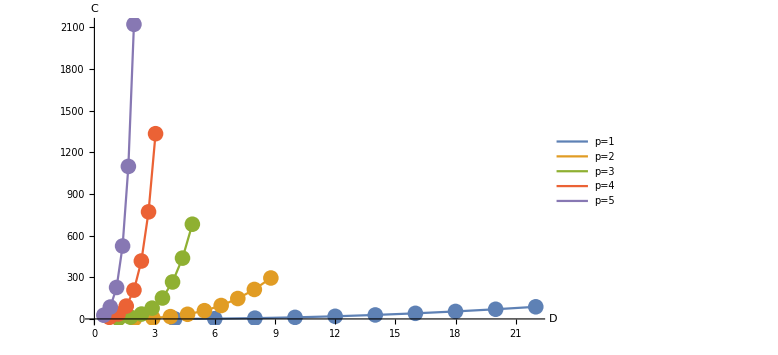

```mathematica
o1=ListLinePlot[data[[1]],Joined->True,PlotLegends->Automatic,AxesLabel->{HoldForm[D],HoldForm[C]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 1",18]];
o2=ListLinePlot[data[[2]],Joined->True,PlotLegends->Automatic,AxesLabel->{HoldForm[D],HoldForm[C]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 2",18]];
o3=ListLinePlot[data[[3]],Joined->True,PlotLegends->Automatic,AxesLabel->{HoldForm[D],HoldForm[C]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 3",18]];
o4=ListLinePlot[data[[4]],Joined->True,PlotLegends->Automatic,AxesLabel->{HoldForm[D],HoldForm[C]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 4",18]];
ListLinePlot[{data[[1]],data[[2]],data[[3]],data[[4]],data[[5]]},Joined->True,PlotLegends->{"p=1","p=2","p=3","p=4","p=5"},AxesLabel->{HoldForm[D],HoldForm[C]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All]
```